# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=xh*.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*D[P[ x, xh],{x,2}]+D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.02, 0.045, 0.1, 0.2};
κs = { 0.5,1, 1.9, 4.9};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
cstar = Flatten[Table[Re[2*κ/(1+Sqrt[1-4*κ*λ])]/.p, {p, params}]]
products = Table[i*j, {i, λs}, {j, κs}]
```

{{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→1.9},{λ→0.02,κ→4.9},{λ→0.045,κ→0.5},{λ→0.045,κ→1},{λ→0.045,κ→1.9},{λ→0.045,κ→4.9},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→1.9},{λ→0.1,κ→4.9},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→1.9},{λ→0.2,κ→4.9}}

{0.505103,1.02084,1.97827,5.50641,0.511787,1.04957,2.09809,7.29432,0.527864,1.12702,2.55051,5.,0.563508,1.38197,2.5,2.5}

{{0.01,0.02,0.038,0.098},{0.0225,0.045,0.0855,0.2205},{0.05,0.1,0.19,0.49},{0.1,0.2,0.38,0.98}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the same initial width for every parameter set: the one with the largest s.s. width in x. Nondimensionalize time κ1 =1 Depends on the noise strengths σx^2, σy^2

```mathematica
λTable =Flatten[ Transpose[Table[λs, 4]]]
```

{0.02,0.02,0.02,0.02,0.045,0.045,0.045,0.045,0.1,0.1,0.1,0.1,0.2,0.2,0.2,0.2}

#### steady-state distribution widths in x~, x

```mathematica
xtwidths = Table[1/κ+((1+κ) λ)/κ/.p, {p, params}]
```

{2.06,1.04,0.556842,0.228163,2.135,1.09,0.595,0.258265,2.3,1.2,0.678947,0.32449,2.6,1.4,0.831579,0.444898}

```mathematica
xwidths = xtwidths/λTable
```

{103.,52.,27.8421,11.4082,47.4444,24.2222,13.2222,5.73923,23.,12.,6.78947,3.2449,13.,7.,4.15789,2.22449}

```mathematica
varChoice=1;
```

```mathematica
xStds = Table[Sqrt[ 1/κ+((1+κ) λ)/κ]/.p,{p, params}]
```

{1.43527,1.0198,0.746219,0.477664,1.46116,1.04403,0.771362,0.508198,1.51658,1.09545,0.823983,0.56964,1.61245,1.18322,0.91191,0.667007}

```mathematica
(*xStds = Table[Sqrt[ 1/κ+((1+κ) λ)/κ]/.params[[varChoice]],Length[params]]*)
xhStds = N[Table[ Sqrt[(1+κ)]/.p, {p, params}]]
```

{1.22474,1.41421,1.70294,2.42899,1.22474,1.41421,1.70294,2.42899,1.22474,1.41421,1.70294,2.42899,1.22474,1.41421,1.70294,2.42899}

#### Boundary condition at y*=1, x* = 2k/(1+Sqrt(1-4*l*k))

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
x0 = 8;
xls=-5*xStds
xrs = x0+5*xStds
xhls=cstar*Sqrt[λs]
xhrs = cstar*x0+5*xhStds
```

{-7.17635,-5.09902,-3.73109,-2.38832,-7.30582,-5.22015,-3.85681,-2.54099,-7.58288,-5.47723,-4.11991,-2.8482,-8.06226,-5.91608,-4.55955,-3.33503}

{15.1764,13.099,11.7311,10.3883,15.3058,13.2202,11.8568,10.541,15.5829,13.4772,12.1199,10.8482,16.0623,13.9161,12.5595,11.335}

{0.141421,0.212132,0.316228,0.447214} {0.505103,1.02084,1.97827,5.50641,0.511787,1.04957,2.09809,7.29432,0.527864,1.12702,2.55051,5.,0.563508,1.38197,2.5,2.5}

{10.1645,15.2378,24.3409,56.1962,10.218,15.4676,25.2994,70.4995,10.3466,16.0872,28.9188,52.145,10.6318,18.1268,28.5147,32.145}

```mathematica
icPos = Table[{x0,x0*c}, {c, cstar}];
icVar = {{1/κ+((1+κ) λ)/κ,1},{1,(1+κ)}}/.params[[varChoice]] ;
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {x, xh}], {pos, icPos}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
(*icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];*)
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcFunc[xl_, xr_, xhl_, xhr_] :={P[xl, xh]==0,
           P[xr, xh]==0,
           P[x, xhr]==0,
           P[x, xhl]==0
}
ΩFunc[xl_, xr_, xhl_, xhr_] :=ImplicitRegion[True,{{x,xl,xr},{xh,xhl,xhr}}];
bcs = MapThread[bcFunc, {xls, xrs, xhrs, xhls}];
minFunc[xStd_, xhStd_]:=Min[6*xStd, 6*xhStd]/300;
cellDistances = MapThread[minFunc, {xStds, xhStds}]
Ω=MapThread[ΩFunc,{xls, xrs, xhls, xhrs}];
```

{0.0244949,0.0282843,0.0287054,0.0287054,0.0244949,0.0282843,0.0287054,0.0287054,0.0244949,0.0282843,0.0287054,0.0287054,0.0244949,0.0282843,0.0287054,0.0287054}

```mathematica
xhCheckFunc[xhl_, c_]:=c≤ xhl
```

```mathematica
MapThread[xhCheckFunc, {cstar*x0-2*xhStds, cstar}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

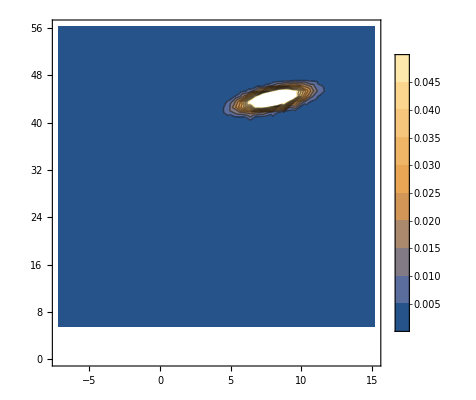

```mathematica
toPlot=4;
ContourPlot[ic0[[toPlot]], {x, xls[[toPlot]], xrs[[toPlot]]}, {xh, xhls[[toPlot]], xhrs[[toPlot]]}, PlotRange->{0, 0.05}, PlotLegends->Automatic]
```

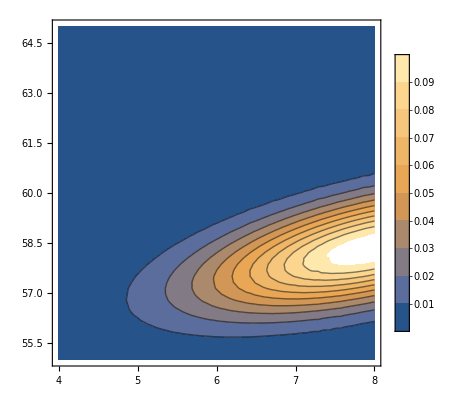

```mathematica
toPlot=8;
ContourPlot[ic0[[toPlot]], {x, 4, 8}, {xh, 55, 65}, PlotRange->{0, 0.1}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{x, xh}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
(*solsSS=MapThread[NDSolverParams, {params, icSS, bcs, meshes}];*)
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

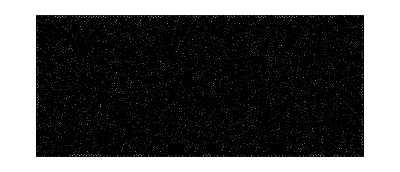

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

```mathematica
(*fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];*)
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

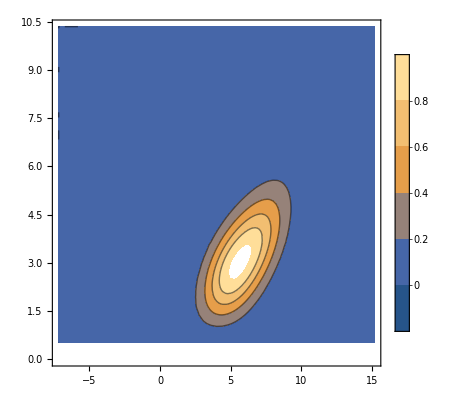

```mathematica
toShow = 9;cIc0 =ContourPlot[solsIc0[[toShow]][x, xh], {x, xls[[toShow]], xrs[[toShow]]}, {xh, xhls[[toShow]], xhrs[[toShow]]}, PlotLegends->Automatic, PlotRange->{-0.01, 1}];
(*Show[cSS]*)
Show[cIc0]
```

```mathematica
XIc0 =MapThread[#1[x,#2]&,{fluxXIc0,cstar}];
```

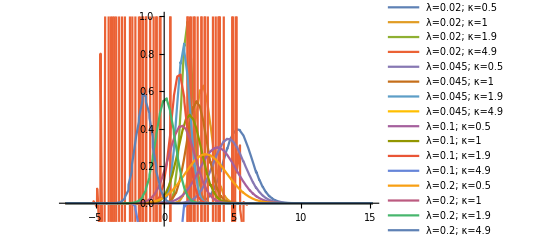

```mathematica
Plot[XIc0, {x, -20, 20}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
(*normsSS = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;*)
```

```mathematica
NIntegrate[XIc0[[1]], {x, 1, 10}, WorkingPrecision->8]
```

0.98968067

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {x, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xls, xrs}]
meansIc0= MapThread[IntegFunc, {XIc0*x, xls, xrs}]
secondIc0 = MapThread[IntegFunc, {XIc0*x*x, xls, xrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

{0.992708136,0.9945576632,1.003258496,-4.178194291×10^19,0.9950445749,0.9978657909,1.003815802,NIntegrate[(P/.{P[x,xh]-4.9 x P^(0,1)[x,xh]+xh P^(0,1)[x,xh]+P^(0,2)[x,xh]+0.045 xh P^(1,0)[x,xh]+0.045 P^(2,0)[x,xh]==-0.11009 2.71828^(0.5 (-1. (-8.+x) (0.717703 (-8.+x)-0.478469 (-58.3546+xh))-1. (-0.478469 (-8.+x)+0.985646 (-58.3546+xh)) (-58.3546+xh))),P[-7.17635,xh]==0,P[15.1764,xh]==0,P[x,7.29432]==0,P[x,70.4995]==0})^(0,1)[x,7.29432],{x,-7.17635,15.1764},WorkingPrecision→10],0.9978873395,1.001945493,1.00049238,-115.7350083,1.000602514,1.001677861,0.9888842267,0.8475186036}

{5.385965254,2.823771171,1.692684128,-4.382811868×10^19,4.73555758,2.39439458,1.411802175,NIntegrate[x (P/.{P[x,xh]-4.9 x P^(0,1)[x,xh]+xh P^(0,1)[x,xh]+P^(0,2)[x,xh]+0.045 xh P^(1,0)[x,xh]+0.045 P^(2,0)[x,xh]==-0.11009 2.71828^(0.5 (-1. (-8.+x) (0.717703 (-8.+x)-0.478469 (-58.3546+xh))-1. (-0.478469 (-8.+x)+0.985646 (-58.3546+xh)) (-58.3546+xh))),P[-7.17635,xh]==0,P[15.1764,xh]==0,P[x,7.29432]==0,P[x,70.4995]==0})^(0,1)[x,7.29432],{x,-7.17635,15.1764},WorkingPrecision→10],3.943699552,1.87870295,1.071798571,38.56941571,3.088772588,1.291468939,0.08043563335,-1.232523995}

{30.27257546,8.435104383,3.036558004,-4.840105535×10^19,23.87081175,6.301701384,2.231465582,NIntegrate[x^2 (P/.{P[x,xh]-4.9 x P^(0,1)[x,xh]+xh P^(0,1)[x,xh]+P^(0,2)[x,xh]+0.045 xh P^(1,0)[x,xh]+0.045 P^(2,0)[x,xh]==-0.11009 2.71828^(0.5 (-1. (-8.+x) (0.717703 (-8.+x)-0.478469 (-58.3546+xh))-1. (-0.478469 (-8.+x)+0.985646 (-58.3546+xh)) (-58.3546+xh))),P[-7.17635,xh]==0,P[15.1764,xh]==0,P[x,7.29432]==0,P[x,70.4995]==0})^(0,1)[x,7.29432],{x,-7.17635,15.1764},WorkingPrecision→10],17.37325726,4.253870574,1.485376729,-34.9631675,11.86065445,2.594028602,0.5023869567,2.08699526}

{1.2639537,0.46142076,0.17137845,-1.92090399×10^39,1.4453062,0.56857598,0.2382802,-NIntegrate[x (P/.{P[x,xh]-4.9 x P^(0,1)[x,xh]+xh P^(0,1)[x,xh]+P^(0,2)[x,xh]+0.045 xh P^(1,0)[x,xh]+0.045 P^(2,0)[x,xh]==-0.11009 2.71828^(0.5 (-1. (-8.+x) (0.717703 (-8.+x)-0.478469 (-58.3546+xh))-1. (-0.478469 (-8.+x)+0.985646 (-58.3546+xh)) (-58.3546+xh))),P[-7.17635,xh]==0,P[15.1764,xh]==0,P[x,7.29432]==0,P[x,70.4995]==0})^(0,1)[x,7.29432],{x,-7.17635,15.1764},WorkingPrecision→10]^2+NIntegrate[x^2 (P/.{P[x,xh]-4.9 x P^(0,1)[x,xh]+xh P^(0,1)[x,xh]+P^(0,2)[x,xh]+0.045 xh P^(1,0)[x,xh]+0.045 P^(2,0)[x,xh]==-0.11009 2.71828^(0.5 (-1. (-8.+x) (0.717703 (-8.+x)-0.478469 (-58.3546+xh))-1. (-0.478469 (-8.+x)+0.985646 (-58.3546+xh)) (-58.3546+xh))),P[-7.17635,xh]==0,P[15.1764,xh]==0,P[x,7.29432]==0,P[x,70.4995]==0})^(0,1)[x,7.29432],{x,-7.17635,15.1764},WorkingPrecision→10],1.8204911,0.7243458,0.33662455,-1522.563,2.3201384,0.926136582,0.495917066,0.567879863}

```mathematica
normsIc0[[8]]=1;
varsIc0[[8]]=1;
meansIc0[[8]]=1;
normsIc0[[4]]=1;
varsIc0[[4]]=1;
meansIc0[[4]]=1;
normsIc0[[12]]=1;
varsIc0[[12]]=1;
meansIc0[[12]]=1;
```

```mathematica
grid = Flatten[Table[{l, s}, {l, λs}, {s, κs}], 1];
params
```

{{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→1.9},{λ→0.02,κ→4.9},{λ→0.045,κ→0.5},{λ→0.045,κ→1},{λ→0.045,κ→1.9},{λ→0.045,κ→4.9},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→1.9},{λ→0.1,κ→4.9},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→1.9},{λ→0.2,κ→4.9}}

```mathematica
(*normArraySS = ArrayReshape[normsSS, {5, 5}];
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];*)
normArrayIc0 = ArrayReshape[normsIc0, {4,4}];
varArrayIc0 = ArrayReshape[varsIc0, {4,4}];
meanArrayIc0 = ArrayReshape[meansIc0, {4,4}];
diffArrayIc0 = ArrayReshape[diffIc0, {4,4}];
```

```mathematica
scaleArray = Transpose[Table[Flatten[Table[l, {l, λs}], 1], 4]]
```

{{0.02,0.02,0.02,0.02},{0.045,0.045,0.045,0.045},{0.1,0.1,0.1,0.1},{0.2,0.2,0.2,0.2}}

```mathematica
scaledVar = varArrayIc0*scaleArray
```

{{0.0252791,0.00922842,0.00342757,0.02},{0.0650388,0.0255859,0.0107226,0.045},{0.182049,0.0724346,0.0336625,0.1},{0.464028,0.185227,0.0991834,0.113576}}

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4}, λs}];
yticks = Transpose[{{1, 2, 3, 4}, κs}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[x]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[scaledVar, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {4,4}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

#### Check that all s.s. variances have been reached before mean passage

```mathematica
S[A_, B_] := FullSimplify[Integrate[MatrixExp[-A*(t-tp)].B.Transpose[B].MatrixExp[-Transpose[A]*(t-tp)], {tp, 0, t}]];
```

```mathematica
As = {{ 0,λ},{-κ, 1}}
Bs = {{Sqrt[2*λ],0},{0,Sqrt[2] }}
s0[λ_, κ_, t_] = FullSimplify[MatrixExp[-{{ 0,λ},{-κ, 1}}*t].icVar.MatrixExp[-Transpose[{{ 0,λ},{-κ, 1}}]*t]]
```

{{0,λ},{-κ,1}}

{{√2 √λ,0},{0,√2}}

{{1/(-0.25+1. κ λ)(ⅇ^-t (-0.5+1.03 κ+0.75 λ) λ+ⅇ^(-t (1+√(1-4 κ λ))) (-0.2575+0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ-0.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-0.2575-0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ+0.25 √(1-4 κ λ)))),1/(-0.25+1. κ λ)(-0.2575 Cosh[t]+0.2575 Sinh[t]) (0.970874-2. κ-1.45631 λ+(κ (2.-3.8835 λ)+1.45631 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.728155 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)])},{1/(-0.25+1. κ λ)(-0.2575 Cosh[t]+0.2575 Sinh[t]) (0.970874-2. κ-1.45631 λ+(κ (2.-3.8835 λ)+1.45631 λ) Cosh[t √(1-4 κ λ)]+2. (1. κ-0.728155 λ) √(1-4 κ λ) Sinh[t √(1-4 κ λ)]),1/(-0.25+1. κ λ)(ⅇ^-t κ (-0.5+1.03 κ+0.75 λ)+ⅇ^(t (-1+√(1-4 κ λ))) (-0.1875+0.1875 √(1-4 κ λ)+κ (0.25-0.515 κ+0.375 λ-0.25 √(1-4 κ λ)))+ⅇ^(-t (1+√(1-4 κ λ))) (-0.1875-0.1875 √(1-4 κ λ)+κ (0.25-0.515 κ+0.375 λ+0.25 √(1-4 κ λ))))}}

```mathematica
curve =S[As, Bs]
```

{{(λ (-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1-2 (-1+κ) λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+2 (-1+κ) λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+4 (1+κ) λ (1-Cosh[t]+Sinh[t])))/(-1+4 κ λ),-(ⅇ^(-t (2+√(1-4 κ λ))) (4 ⅇ^(t (1+√(1-4 κ λ))) (1+κ) λ+ⅇ^(t (2+√(1-4 κ λ))) (2-8 κ λ)-ⅇ^(t+2 t √(1-4 κ λ)) (1-2 (-1+κ) λ+√(1-4 κ λ))+ⅇ^t (-1+2 (-1+κ) λ+√(1-4 κ λ))))/(2 (-1+4 κ λ))},{-(ⅇ^(-t (2+√(1-4 κ λ))) (4 ⅇ^(t (1+√(1-4 κ λ))) (1+κ) λ+ⅇ^(t (2+√(1-4 κ λ))) (2-8 κ λ)-ⅇ^(t+2 t √(1-4 κ λ)) (1-2 (-1+κ) λ+√(1-4 κ λ))+ⅇ^t (-1+2 (-1+κ) λ+√(1-4 κ λ))))/(2 (-1+4 κ λ)),(-((1-ⅇ^(-t (1+√(1-4 κ λ)))) (1+2 (-1+κ) κ λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+1/2 (-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1+κ-√(1-4 κ λ)+κ √(1-4 κ λ))+4 κ (1+κ) λ (1-Cosh[t]+Sinh[t]))/(-1+4 κ λ)}}

```mathematica
toPlotCurve[λ_, κ_, t_]=(s0+(λ (-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1-2 (-1+κ) λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+2 (-1+κ) λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+4 (1+κ) λ (1-Cosh[t]+Sinh[t])))/(-1+4 κ λ))[[1,1]]
```

1/(-0.25+1. κ λ)(ⅇ^-t (-0.5+1.03 κ+0.75 λ) λ+ⅇ^(-t (1+√(1-4 κ λ))) (-0.2575+0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ-0.25 √(1-4 κ λ)))+ⅇ^(t (-1+√(1-4 κ λ))) (-0.2575-0.2575 √(1-4 κ λ)+λ (0.25+0.515 κ-0.375 λ+0.25 √(1-4 κ λ))))+(λ (-((-1+ⅇ^(t (-1+√(1-4 κ λ)))) (1-2 (-1+κ) λ+√(1-4 κ λ)))/(-1+√(1-4 κ λ))+((1-ⅇ^(-t (1+√(1-4 κ λ)))) (-1+2 (-1+κ) λ+√(1-4 κ λ)))/(1+√(1-4 κ λ))+4 (1+κ) λ (1-Cosh[t]+Sinh[t])))/(-1+4 κ λ)

```mathematica
Manipulate[Plot[{toPlotCurve[λ, κ, t],  1/κ+((1+κ) λ)/κ}, {t, 0, 30}, PlotRange->{0, 10}, GridLines->{{{tfPlot [λ, κ, 8],Red}},None}], {λ, 0.02, 0.2}, {κ, 0.2, 2}]
```

```mathematica
tfPlot [λ_, κ_, x0_] := (1/λ)*Log[x0/(2*κ/(1+Sqrt[1-4*λ*κ]))]
```